## Cell Volume 10^-15Regulated System

```mathematica
(*PROGRAM MADE BY KANISHK ASTHANA ka112@duke.edu for BME 574 "Gene Circuits"*)
(*Note to Dr. You:
Dr. You, I've done the simulation in Mathematica by storing the Values of TetR over the time course of the Simulation. I could not find a way to plot the data to without storing the numbers in an Array. I will try to do so in the future. In case your memory runs out during this simulation I have marked the areas of code you can delete to see at least the time course of the Number of Molecules of TetR without plotting the Graph*) 
(*Go to Evaluation-> Evaluate Notebook to begin Simulation*)
(* Defining Initial Molecule Numbers*)
Clear["Global`*"]
Na=6.022*10^23;(*Avogadro's Number*)
CellVolume=1*10^-15;
Nr=0;(*Number of Molecules of TetR *)
No=Floor[(2*10^-7)*(CellVolume)*(Na)];(* No=Molarity*Volume of Cell*Avogadro's Number*)(*Number of Operator sites*)
Nro=0;(* Number of RO complexes*)
(* Defining Reaction Coefficients *) 
Kf=10^8;
Kr=0.01;
KR=0.1;
Kd=10^-4;
(*Defining Reaction Propensities*)
(* Note := is Delayed assignment operator, thus values or both LHS and RHS are linked, therefore Value a1 will change automatically as value of Nr and No changes*) 

a1:=Kf/(Na * CellVolume) Nr* No
a2:= Kr*Nro
a3:=KR*No
a4:=Kd*Nr
a0:=a1+a2+a3+a4
t=0;
maxiteration=200000;(* Number of Iterations over which loop will be executed *)
Print["Time Passed since start of Session:"]
SessionTime[]
```

Time Passed since start of Session:

3493.246

```mathematica
Print["The Dynamic Value of Number of Molecules of TetR is:"]       
Dynamic[Nr](*The output of this line of code will show the Value of Nr changing over the time course of the simulation. So this can show the value of Number of TetR molecules changing over time even if the values stored in the array below cannot *)
(*Starting Loop *)
For[i=1,i<maxiteration+1,i++, 
 (*Note Please delete next two lines of Code if the memory runs out during the simulation *) 
 Set[NrT[i,1],t](*Storing Current time point as First element of Array*)
Set[NrT[i,2],Nr](*Storing Current Value of Nr(Number of TetR Molecules) in as second element of an Array *)
Set[r2,Random[]](*Generating Random Number with values between 0 and 1 and storing in variable r2*)
Set[dt,(-Log[Random[]]/a0)](* Generating Random time step and storing in variable dt*)
(*Selecting Which reaction to "Fire" on the Basis of the value of r2*)
(* Variable++ is equivalent to the assignment Variable=Variable+1*)
If[0<r2≤N[(a1/a0)],
t=t+dt
Nro++
Nr--
No--
 ]
If[N[(a1/a0)]< r2≤ N[((a2+a1)/a0)],
t=t+dt 
Nro--
Nr++
No++
        ]
If[N[((a2+a1)/a0)]<r2≤N[((a3+a2+a1)/a0)],
t=t+dt
Nr++
]
If[N[((a3+a2+a1)/a0)]<r2≤ N[((a4+a3+a2+a1)/a0)],
Nr--
t=t+dt
]

]
```

The Dynamic Value of Number of Molecules of TetR is:

Set::write: Tag Times in 28\ 430765. is Protected.

Set::write: Tag Times in 46\ 1.51243×10^6 is Protected.

Set::write: Tag Times in 54\ 2.03113×10^6 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

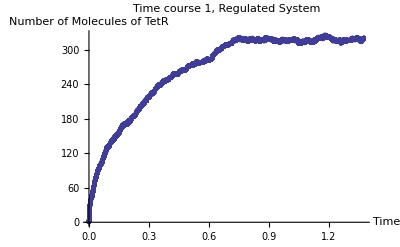

```mathematica
ListPlot[Array[NrT,{maxiteration,2}],PlotRange->Full,Joined->False,AxesLabel->{"Time","Number of Molecules of TetR"},PlotLabel->"Time course 1, Regulated System"](* Plot of Time Course of Simulation *)
(*Steady state is acheived at around 320 Molecules of TetR and between 125000 and 150000 iterations*)
```

```mathematica
?Set
?ListPlot
```

RowBox[{StyleBox["lhs", "TI"], "=", StyleBox["rhs", "TI"]}] evaluates StyleBox["rhs", "TI"] and assigns the result to be the value of StyleBox["lhs", "TI"]. From then on, StyleBox["lhs", "TI"] is replaced by StyleBox["rhs", "TI"] whenever it appears. 
RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["l", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["l", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "=", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}] evaluates the SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]], and assigns the results to be the values of the corresponding SubscriptBox[StyleBox["l", "TI"], StyleBox["i", "TI"]].

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
(* Extracting last values from last 20000 iterations to find mean and standard deviation and storing in Table Dist *)

Dist=Table[NrT[i,2],{i,160000,200000}];
```

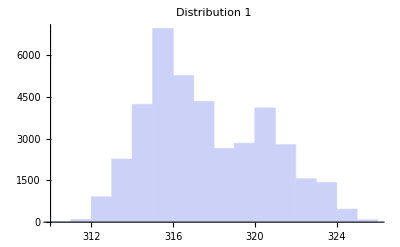

The Mean is:

317

The Standard Deviation is:

2

RowBox[{"Floor", "[", StyleBox["x", "TI"], "]"}] gives the greatest integer less than or equal to StyleBox["x", "TI"]. 
RowBox[{"Floor", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["a", "TI"]}], "]"}] gives the greatest multiple of StyleBox["a", "TI"] less than or equal to StyleBox["x", "TI"].

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

```mathematica
Histogram[Dist,PlotLabel->"Distribution 1"](*Range of Values during steady state*)
Print["The Mean is:"]
Floor[N[Mean[Dist]]] (*Finding Numerical Value of Mean of Distribution rounded to nearest integer*)
Print["The Standard Deviation is:"]
Floor[N[StandardDeviation[Dist]]](* Findind Numerical Value of Standard Deviation of Distribution to nearest integer*)
?Floor
?N
```

## Cell Volume 10^-15 Unregulated System

```mathematica
(*Second Part of Simulation Unregulated System *)
Clear["Global`*"]
Na=6.022*10^23;(*Avogadro's Number*)
CellVolume=1*10^-15;
Nr=0;(*Number of Molecules of TetR *)
No=Floor[(2*10^-7)*(CellVolume)*(Na)];(* No=Molarity*Volume of Cell*Avogadro's Number*)(*Number of Operator sites rounded to nearest integer*)
(* Defining Reaction Coefficients *) 

KR=7.07*10^-5;(*Scaling Rate constants to give same steady state level*)
Kd=10^-4;
(*Defining Reaction Propensities*)
(* Note := is Delayed assignment operator, thus values or both LHS and RHS are linked, therefore Value a1 will change automatically as value of Nr and No changes*) 

a3:=KR*No
a4:=Kd*Nr
a0:=a3+a4
t=0;
maxiteration=200000;(* Number of Iterations over which loop will be executed *)
Print["Time Passed since start of Session:"]
SessionTime[]
```

Time Passed since start of Session:

3561.979

```mathematica
Print["The Dynamic Value of Number of Molecules of TetR is:"]       
Dynamic[Nr](*The output of this line of code will show the Value of Nr changing over the time course of the simulation. So this can show the value of Number of TetR molecules changing over time even if the values stored in the array below cannot *)
(*Starting Loop *)
For[i=1,i<maxiteration+1,i++, 
 (*Note Please delete next two lines of Code if the memory runs out during the simulation *) 
 Set[NrT[i,1],t](*Storing Current time point as First element of Array*)
Set[NrT[i,2],Nr](*Storing Current Value of Nr(Number of TetR Molecules) in as second element of an Array *)
Set[r2,Random[]](*Generating Random Number with values between 0 and 1 and storing in variable r2*)
Set[dt,(-Log[Random[]]/a0)](* Generating Random time step and storing in variable dt*)
(*Selecting Which reaction to "Fire" on the Basis of the value of r2*)
(* Variable++ is equivalent to the assignment Variable=Variable+1*)
If[0<r2≤N[(a3/a0)],
t=t+dt
Nr++
 ]
If[N[(a3/a0)]< r2≤ N[((a3+a4)/a0)],
t=t+dt 
Nr--
        ]


]
```

The Dynamic Value of Number of Molecules of TetR is:

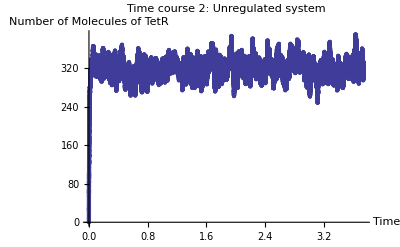

```mathematica
ListPlot[Array[NrT,{maxiteration,2}],PlotRange->Full,Joined->False,AxesLabel->{"Time","Number of Molecules of TetR"},PlotLabel->"Time course 2: Unregulated system"](* Plot of Time Course of Simulation *)
(*Steady state is acheived at around 88 Molecules of TetR*)
```

```mathematica
(* Extracting last values from last 20000 iterations to find mean and standard deviation and storing in Table Dist *)

Dist=Table[NrT[i,2],{i,160000,200000}];
```

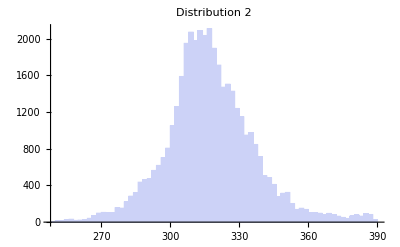

The Mean is:

316

The Standard Deviation is:

19

RowBox[{"Floor", "[", StyleBox["x", "TI"], "]"}] gives the greatest integer less than or equal to StyleBox["x", "TI"]. 
RowBox[{"Floor", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["a", "TI"]}], "]"}] gives the greatest multiple of StyleBox["a", "TI"] less than or equal to StyleBox["x", "TI"].

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

```mathematica
Histogram[Dist,PlotLabel->"Distribution 2"](*Range of Values during steady state*)
Print["The Mean is:"]
Floor[N[Mean[Dist]]] (*Finding Numerical Value of Mean of Distribution rounded to nearest integer*)
Print["The Standard Deviation is:"]
Floor[N[StandardDeviation[Dist]]](* Findind Numerical Value of Standard Deviation of Distribution to nearest integer*)
?Floor
?N
```

```mathematica
(* Comment Looking at Distribution 1 and Distribution 2 as well as Time course 1 and Time course 2. The following things are evident from the Simulation:
1. That the amount of time taken to read steady state is much higher for the same steady state in the Regulated system
2. The regulated system has much less noise as compared to the unregulated system
*)
```

## Cell Volume 10^-13 Regulated Sytem

```mathematica
(* Defining Initial Molecule Numbers*)
Clear["Global`*"]
Na=6.022*10^23;(*Avogadro's Number*)
CellVolume=1*10^-13;
Nr=0;(*Number of Molecules of TetR *)
No=Floor[(2*10^-7)*(CellVolume)*(Na)];(* No=Molarity*Volume of Cell*Avogadro's Number*)(*Number of Operator sites*)
Nro=0;(* Number of RO complexes*)
(* Defining Reaction Coefficients *) 
Kf=10^8;
Kr=0.01;
KR=0.1;
Kd=10^-4;
(*Defining Reaction Propensities*)
(* Note := is Delayed assignment operator, thus values or both LHS and RHS are linked, therefore Value a1 will change automatically as value of Nr and No changes*) 

a1:=Kf/(Na * CellVolume) Nr* No
a2:= Kr*Nro
a3:=KR*No
a4:=Kd*Nr
a0:=a1+a2+a3+a4
t=0;
maxiteration=350000;(* Number of Iterations over which loop will be executed, takes much longer to attain steady state *)
Print["Time Passed since start of Session:"]
SessionTime[]

Print["The Dynamic Value of Number of Molecules of TetR is:"]
       
Dynamic[Nr](*The output of this line of code will show the Value of Nr changing over the time course of the simulation. So this can show the value of Number of TetR molecules changing over time even if the values stored in the array below cannot *)
(*Starting Loop *)
For[i=1,i<maxiteration+1,i++, 
 (*Note Please delete next two lines of Code if the memory runs out during the simulation *) 
 Set[NrT[i,1],t](*Storing Current time point as First element of Array*)
Set[NrT[i,2],Nr](*Storing Current Value of Nr(Number of TetR Molecules) in as second element of an Array *)
Set[r2,Random[]](*Generating Random Number with values between 0 and 1 and storing in variable r2*)
Set[dt,(-Log[Random[]]/a0)](* Generating Random time step and storing in variable dt*)
(*Selecting Which reaction to "Fire" on the Basis of the value of r2*)
(* Variable++ is equivalent to the assignment Variable=Variable+1*)
If[0<r2≤N[(a1/a0)],
t=t+dt
Nro++
Nr--
No--
 ]
If[N[(a1/a0)]< r2≤ N[((a2+a1)/a0)],
t=t+dt 
Nro--
Nr++
No++
        ]
If[N[((a2+a1)/a0)]<r2≤N[((a3+a2+a1)/a0)],
t=t+dt
Nr++
]
If[N[((a3+a2+a1)/a0)]<r2≤ N[((a4+a3+a2+a1)/a0)],
Nr--
t=t+dt
]

]
ListPlot[Array[NrT,{maxiteration,2}],PlotRange->Full,Joined->False,AxesLabel->{"Time","Number of Molecules of TetR"},PlotLabel->"Time course 1, Regulated System"]
(* Plot of Time Course of Simulation *)
(*Steady state is acheived at around 320 Molecules of TetR and between 125000 and 150000 iterations*)
```

Time Passed since start of Session:

3902.414

The Dynamic Value of Number of Molecules of TetR is:

Set::write: Tag Times in 641\ 7.05648×10^10 is Protected.

Set::write: Tag Times in 648\ 7.10356×10^10 is Protected.

Set::write: Tag Times in 670\ 7.28914×10^10 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

-Graphics-

```mathematica
(*NOTE: In this case the computer did not have enough memory to allow the simulation to complete, however even at this early stage it is evident that the simultaion may take upto 100 times longer to reach steady state. The steady state number of molecules should also increase 100 fold as seen in the case for the Unregualted simulation *)
?Set
?ListPlot
```

RowBox[{StyleBox["lhs", "TI"], "=", StyleBox["rhs", "TI"]}] evaluates StyleBox["rhs", "TI"] and assigns the result to be the value of StyleBox["lhs", "TI"]. From then on, StyleBox["lhs", "TI"] is replaced by StyleBox["rhs", "TI"] whenever it appears. 
RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["l", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["l", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "=", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}] evaluates the SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]], and assigns the results to be the values of the corresponding SubscriptBox[StyleBox["l", "TI"], StyleBox["i", "TI"]].

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
(* Extracting last values from last 20000 iterations to find mean and standard deviation and storing in Table Dist *)

Dist=Table[NrT[i,2],{i,330000,350000}];
```

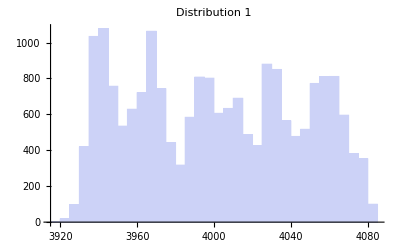

The Mean is:

4000

The Standard Deviation is:

43

RowBox[{"Floor", "[", StyleBox["x", "TI"], "]"}] gives the greatest integer less than or equal to StyleBox["x", "TI"]. 
RowBox[{"Floor", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["a", "TI"]}], "]"}] gives the greatest multiple of StyleBox["a", "TI"] less than or equal to StyleBox["x", "TI"].

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

```mathematica
Histogram[Dist,PlotLabel->"Distribution 1"](*Range of Values during steady state*)
Print["The Mean is:"]
Floor[N[Mean[Dist]]] (*Finding Numerical Value of Mean of Distribution rounded to nearest integer*)
Print["The Standard Deviation is:"]
Floor[N[StandardDeviation[Dist]]](* Findind Numerical Value of Standard Deviation of Distribution to nearest integer*)
?Floor
?N
```

## Cell Volume 10^-13Unregulated System

```mathematica
(*Second Part of Simulation Unregulated System *)
Clear["Global`*"]
Na=6.022*10^23;(*Avogadro's Number*)
CellVolume=1*10^-13;
Nr=0;(*Number of Molecules of TetR *)
No=Floor[(2*10^-7)*(CellVolume)*(Na)];(* No=Molarity*Volume of Cell*Avogadro's Number*)(*Number of Operator sites rounded to nearest integer*)
(* Defining Reaction Coefficients *) 

KR=7.07*10^-5;(*Scaling Rate constants to give same steady state level*)
Kd=10^-4;
(*Defining Reaction Propensities*)
(* Note := is Delayed assignment operator, thus values or both LHS and RHS are linked, therefore Value a1 will change automatically as value of Nr and No changes*) 

a3:=KR*No
a4:=Kd*Nr
a0:=a3+a4
t=0;
maxiteration=350000;(* Number of Iterations over which loop will be executed, takes more iterations to reach steady state *)
Print["Time Passed since start of Session:"]
SessionTime[]
```

Time Passed since start of Session:

4014.259

```mathematica
Print["The Dynamic Value of Number of Molecules of TetR is:"]       
Dynamic[Nr](*The output of this line of code will show the Value of Nr changing over the time course of the simulation. So this can show the value of Number of TetR molecules changing over time even if the values stored in the array below cannot *)
(*Starting Loop *)
For[i=1,i<maxiteration+1,i++, 
 (*Note Please delete next two lines of Code if the memory runs out during the simulation *) 
 Set[NrT[i,1],t](*Storing Current time point as First element of Array*)
Set[NrT[i,2],Nr](*Storing Current Value of Nr(Number of TetR Molecules) in as second element of an Array *)
Set[r2,Random[]](*Generating Random Number with values between 0 and 1 and storing in variable r2*)
Set[dt,(-Log[Random[]]/a0)](* Generating Random time step and storing in variable dt*)
(*Selecting Which reaction to "Fire" on the Basis of the value of r2*)
(* Variable++ is equivalent to the assignment Variable=Variable+1*)
If[0<r2≤N[(a3/a0)],
t=t+dt
Nr++
 ]
If[N[(a3/a0)]< r2≤ N[((a3+a4)/a0)],
t=t+dt 
Nr--
        ]


]
```

The Dynamic Value of Number of Molecules of TetR is:

```mathematica
ListPlot[Array[NrT,{maxiteration,2}],PlotRange->Full,Joined->False,AxesLabel->{"Time","Number of Molecules of TetR"},PlotLabel->"Time course 2: Unregulated system"](* Plot of Time Course of Simulation *)
(*Steady state is acheived at around 88 Molecules of TetR*)
```

-Graphics-

```mathematica
(* Extracting last values from last 20000 iterations to find mean and standard deviation and storing in Table Dist *)

Dist=Table[NrT[i,2],{i,330000,350000}];
```

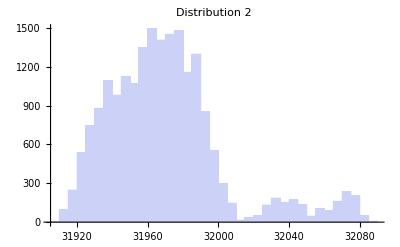

The Mean is:

31969

The Standard Deviation is:

33

RowBox[{"Floor", "[", StyleBox["x", "TI"], "]"}] gives the greatest integer less than or equal to StyleBox["x", "TI"]. 
RowBox[{"Floor", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["a", "TI"]}], "]"}] gives the greatest multiple of StyleBox["a", "TI"] less than or equal to StyleBox["x", "TI"].

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

```mathematica
Histogram[Dist,PlotLabel->"Distribution 2"](*Range of Values during steady state*)
Print["The Mean is:"]
Floor[N[Mean[Dist]]] (*Finding Numerical Value of Mean of Distribution rounded to nearest integer*)
Print["The Standard Deviation is:"]
Floor[N[StandardDeviation[Dist]]](* Findind Numerical Value of Standard Deviation of Distribution to nearest integer*)
?Floor
?N
```

```mathematica
Print["Time Passed since start of Session:"]
SessionTime[]
```

Time Passed since start of Session:

4056.861